```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Define the metric and its inverse to Order(orderexp)*)
orderexp=2;
tt=-(1-(2 M r[s])/(r[s]^2+a^2 Cos[θ[s]]^2));
rr=(r[s]^2+a^2 Cos[θ[s]]^2)/(r[s]^2-2 M r[s]+a^2);
θθ=r[s]^2+a^2 Cos[θ[s]]^2;
ϕϕ=Sin[θ[s]]^2(r[s]^2+a^2+(2M a^2 r[s] Sin[θ[s]]^2)/(r[s]^2+a^2 Cos[θ[s]]^2));
tϕ=-((2 a M r[s] Sin[θ[s]]^2)/(r[s]^2+a^2 Cos[θ[s]]^2));
metric=Normal[Series[{{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}},{a,0,orderexp}]];
inversemetric=Normal[Series[Inverse[metric],{a,0,orderexp}]];
```

```mathematica
(*Define the relativistic Hamiltonian and the equations of motion to Order(orderexp)*)
H=Normal[Series[1/(2μ)(inversemetric[[2,2]](Pr[s]^2)+inversemetric[[3,3]](Pθ[s]^2)-2inversemetric[[1,4]](μ^2  EE*L)+inversemetric[[4,4]](μ^2 L^2 )+inversemetric[[1,1]](μ^2  EE^2)),{a,0,orderexp}]];
tp=Normal[Series[-Chop[D[H,EE]],{a,0,orderexp}]];
ϕp=Normal[Series[Chop[D[H,L]],{a,0,orderexp}]];
Pmr=Normal[Series[Chop[-D[H,r[s]]],{a,0,orderexp}]];
Pmθ=Normal[Series[Chop[-D[H,θ[s]]],{a,0,orderexp}]];
rcp=Normal[Series[Chop[D[H,Pr[s]]],{a,0,orderexp}]];
θcp=Normal[Series[Chop[D[H,Pθ[s]]],{a,0,orderexp}]];
```

```mathematica
(*Initial Values*)
M=1;
L=3.75365;(*Initial Angular Momentum*)
EE=0.995;(*Initial energy*)
μ=1; (*Rest mass of the particle*)
a=0.2/M; (*spin value*)
```

```mathematica
Halt=H/.r[s]-> r0/.θ[s]-> θ/.Pr[s]-> Pri/.Pθ[s]-> Pθi;(*Evaluate the Hamiltonian with these values*)
```

```mathematica
(*Initial coniditions*)
ri=4.017;(*Initial radius*)
Pri=0;(*We start at a turn in the orbit*)
θi=π/2;(*We start in the equator*)
(*Use the Hamiltonian, which is a constant, to solve for the component left*)
PθIC=NSolve[Evaluate[Halt/.θ-> θi/.r0-> ri]==(-(1/2)μ),Pθi][[2]][[1]][[2]];
```

```mathematica
(*Visualization*)
tMaxPlot=130000;
orbit=NDSolve[{Pr'[s]==Pmr/tp,Pθ'[s]==Pmθ/tp,θ'[s]==θcp/tp,r'[s]==rcp/tp,ϕ'[s]==ϕp/tp,t'[s]==tp,Pr[0]==0,Pθ[0]==PθIC,θ[0]==π/2,r[0]==ri,ϕ[0]==0,t[0]==0},{Pr,Pθ,r,θ,ϕ,t},{s,0,tMaxPlot},Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},AccuracyGoal->16,PrecisionGoal->16,StartingStepSize->0.01,MaxSteps->∞];
```

```mathematica
ParametricPlot3D[{r[s] Sin[θ[s]] Cos[ϕ[s]],r[s] Sin[θ[s]] Sin[ϕ[s]],r[s] Cos[θ[s]]}/.orbit,{s,0,tMaxPlot},PlotRange->All,PlotStyle->{Black,Thick},PlotPoints->100,ViewPoint->{0,0,15}]
```

-Graphics3D-

```mathematica
(*The evolution time to get the phase portrait typically has to be very large*)tsteps=20000000;
```

```mathematica
PoincareSurface=SetPrecision[Reap[NDSolve[{Pr'[s]==Pmr,Pθ'[s]==Pmθ,θ'[s]==θcp,r'[s]==rcp,Pr[0]==0,Pθ[0]==PθIC,θ[0]==π/2,r[0]==ri,WhenEvent[Chop[Cos[θ[s]]]==0,Sow[{Re[r[s]],Re[Pr[s]]}],"LocationMethod"->{"Brent", AccuracyGoal ->16, PrecisionGoal -> 16}]},{},{s,0,tsteps},Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},AccuracyGoal->16,PrecisionGoal->16,StartingStepSize->0.1,MaxSteps->∞]],32][[-1,1]];
```

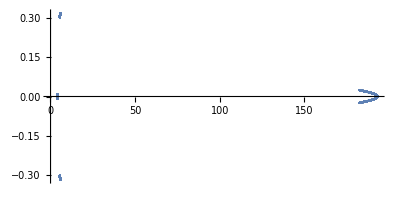

```mathematica
ListPlot[{PoincareSurface},AspectRatio->0.5,PlotRange->All]
```

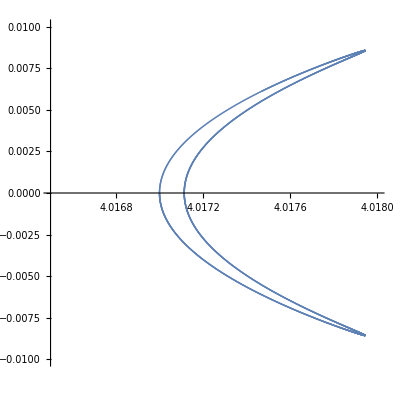

```mathematica
ListPlot[{PoincareSurface},AspectRatio->1,PlotRange->{{4.0165,4.018},{-0.01,0.01}}]
```